# EigenFunctions

## Tyson Jones tyson.jones@monash.edu August 2017

## WavefunctionSolver Package Test

```mathematica
Clear["Global`*"]
```

## Import

The location of the folder containing the package must be added to the paclet directories

In rare circumstances, the PacletManager` context will not be known, and must be prepended to the below call

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< WavefunctionSolver`
```

The available functions and their options:

```mathematica
?WavefunctionSolver`*
```

## One Dimension

## Normalizing wavefunctions

### constants

Passing a domain means the wavefunction is assumed to drop to 0 from the constant value outside the domain

```mathematica
NormalizeWavefunction[10 ⅈ + 14, {x, 0, 10}]
Integrate[Abs[%]^2, {x, 0, 10}]
```

(7/2+(5 ⅈ)/2)/(√185)

1

```mathematica
NormalizeWavefunction[-4, {-5, 5}]
Integrate[Abs[%]^2, {x, -5, 5}]
```

-1/(√10)

1

Constants normalise to 0 on infinite domains

```mathematica
NormalizeWavefunction[2, {-∞, ∞}]
NormalizeWavefunction[2, {-∞, 4}]
```

0

0

A [0, 1] domain is assumed when a constant and no domain is passed

```mathematica
NormalizeWavefunction[4]
```

4

### vectors

Passing a vector of wavefunction values and a grid-spacing (positive real num) assumes the wavefunction is zero outside the length grid-spacing * (Length[vector] - 1) domain

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},   (* wavefunction values *)
	1                                              (* grid spacing *)
]
1 * Total[ Abs[%]^2]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

1

Passing vectors (wavefunction values and their grid positions; must be consistent/equally-spaced) assumes the wavefunction is zero outside [grid[[1]], grid[[-1]]]

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{0, 1, 2, 3, 4, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

Passing a vector of wavefunction values and a domain assumes the wavefunction is zero outside the domain

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{ 0, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

(a redundant Symbol can be passed, to clarify the dimension)

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{x, 0, 5}
]
```

{0,1/(√55),2/(√55),3/(√55),4/(√55),√(5/11)}

(any finite vector will normalise to 0 on an infinite domain)

```mathematica
NormalizeWavefunction[
	{0, 1, 2, 3, 4, 5},
	{ -∞, 5}
]
```

{0,0,0,0,0,0}

Passing no grid-spacing/grid/domain will assume a grid-spacing of 1, and that the wavefunction vanishes outside the length Length[vector]-1 domain

```mathematica
NormalizeWavefunction[
	{1, 2, 3}
]
1 * Total[ Abs[%]^2]
```

{1/(√14),√(2/7),3/(√14)}

1

### functions

A passed function is assumed 0 outside the passed domain

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	{-1, 1}
]

NIntegrate[Abs[%[x]]^2, {x, -1, 1}]
```

((Exp[-#1^2]&)[#1])/1.09375&

1.

Passing a function and a grid will normalise using (bad) Riemann Summation, sampling the function on the grid

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	Table[i, {i, -1, 1, .001}]
]
NIntegrate[Abs[%[x]]^2, {x, -1, 1}]
```

((Exp[-#1^2]&)[#1])/1.09381&

0.999887

Passing a function and no domain will result in an assumed (-∞, ∞) domain

```mathematica
NormalizeWavefunction[
	(Exp[-#^2]&),
	{ -∞, ∞}
]
NIntegrate[Abs[%[x]]^2, {x, -∞, ∞}]
```

((Exp[-#1^2]&)[#1])/1.11952&

1.

```mathematica
NormalizeWavefunction[
	Function[x, Exp[-x^2]]
]
```

(Function[x,Exp[-x^2]][#1])/1.11952&

### symbolic expressions

Symbolic expressions are assumed 0 outside the passed domain

```mathematica
NormalizeWavefunction[
	x Exp[-x^2],
	{x, -5, 5}
]

Integrate[Abs[%]^2, {x, -5, 5}]
```

2 ⅇ^(25-x^2) x √(2/(-20+ⅇ^50 √(2 π) Erf[5 √2]))

1

```mathematica
NormalizeWavefunction[
	x Exp[-x^2],
	{x, -∞, ∞}
]

Integrate[Abs[%]^2, {x, -∞, ∞}]
```

2 ⅇ^(-x^2) (2/π)^(1/4) x

1

Passing no domain (passing only the Symbol, or a list containing only a Symbol) will assume a (-∞, ∞) domain

```mathematica
NormalizeWavefunction[x Exp[-x^2], x]
NormalizeWavefunction[x Exp[-x^2], {x}]
```

2 ⅇ^(-x^2) (2/π)^(1/4) x

2 ⅇ^(-x^2) (2/π)^(1/4) x

### Won’t Match

The length of the vector does not match the length of the grid

```mathematica
NormalizeWavefunction[
	{1, 2, 3, 4, 5},
	{1, 2, 3}
]
```

NormalizeWavefunction[{1,2,3,4,5},{1,2,3}]

### Throws Errors

Symbolic normalisation will throw an error on functions which aren’t L2-normalisable (e.g. feature a singularity, or don’t converge quickly enough to 0 at the infinite boundaries)

```mathematica
(* diverges at x=0 *)
NormalizeWavefunction[
	1/x,
	{x, -1, 1}
]
```

Integrate::idiv: Integral of 1/x^2 does not converge on {-1,1}.

1/(x √(∫_-1^1 1/Abs[x]^2 ⅆx))

```mathematica
(* diverges at x -> infinity *)
NormalizeWavefunction[
	Exp[x],
	{x, 1, ∞}
]
```

Integrate::idiv: Integral of ⅇ^(2 x) does not converge on {1,∞}.

ⅇ^x/(√(∫_1^∞ ⅇ^(2 Re[x])ⅆx))

```mathematica
(* doesn't converge as x -> infinity *)
NormalizeWavefunction[
	Sin[x],
	{x, 1, ∞}
]
```

Integrate::idiv: Integral of Sin[x]^2 does not converge on {1,∞}.

Sin[x]/(√(∫_1^∞ Abs[Sin[x]]^2 ⅆx))

```mathematica
(* doesn't converge to 0 at x -> infinity *)
NormalizeWavefunction[
	Exp[-x] + 1,
	{x, 1, ∞}
]
```

Integrate::idiv: Integral of 1+ⅇ^(-2 x)+2 ⅇ^-x does not converge on {1,∞}.

(1+ⅇ^-x)/(√(∫_1^∞ Abs[1+ⅇ^-x]^2 ⅆx))

```mathematica
(* doesn't converge to 0 quickly enough as x -> infinity *)
NormalizeWavefunction[
	1/Sqrt[x],
	{x,1, ∞}
]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

1/(√x √(∫_1^∞ 1/Abs[x]ⅆx))

Since Functions and InterpolatingFunctions are normalised numerically, input (with a corresponding probability density...) which diverges on the domain or which doesn’t converge quickly enough to 0 at infinite boundaries, will throw errors

```mathematica
(* diverges at x=0 *)
NormalizeWavefunction[
	(1/# &),
	{-1, 1}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in WavefunctionSolver`EigenFunctions`PackagePrivate`x near {WavefunctionSolver`EigenFunctions`PackagePrivate`x} = {0.00387517}. NIntegrate obtained 96177.5 and 80502.5 for the integral and error estimates.

((1/#1&)[#1])/310.125&

```mathematica
(* diverges at x -> +- infinity *)
NormalizeWavefunction[
	(Exp[ #1^2]&),
	{ -∞, ∞}
]
```

NIntegrate::inumri: The integrand ⅇ^(2 Re[(WavefunctionSolver`EigenFunctions`PackagePrivate`x)^2]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.23043×10^7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

(Exp[#1^2]&)[#1]/(√NIntegrate[Abs[(Exp[#1^2]&)[WavefunctionSolver`EigenFunctions`PackagePrivate`x]]^2,{WavefunctionSolver`EigenFunctions`PackagePrivate`x,-∞,∞},Method→{Automatic,SymbolicProcessing→0}])&

```mathematica
(* doesn't converge as x -> infinity *)
NormalizeWavefunction[
	Sin[#]&,
	{x, 1, ∞}
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in WavefunctionSolver`EigenFunctions`PackagePrivate`x near {WavefunctionSolver`EigenFunctions`PackagePrivate`x} = {6.3887×10^56}. NIntegrate obtained 9.57805×10^241 and 9.44088×10^241 for the integral and error estimates.

((Sin[#1]&)[#1])/(9.78675×10^120)&

```mathematica
(* doesn't converge to 0 at x -> infinity *)
NormalizeWavefunction[
	Exp[-#] + 1&,
	{ 1, ∞}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in WavefunctionSolver`EigenFunctions`PackagePrivate`x near {WavefunctionSolver`EigenFunctions`PackagePrivate`x} = {8.16907×10^224}. NIntegrate obtained 8.58263912306054×10^27949 and 8.58263912306054×10^27949 for the integral and error estimates.

((Exp[-#1]+1&)[#1])/(9.264253409239486×10^13974)&

```mathematica
(* doesn't converge to 0 quickly enough as x -> infinity *)
NormalizeWavefunction[
	Function[x, 1/Sqrt[x]],
	{1, ∞}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in WavefunctionSolver`EigenFunctions`PackagePrivate`x near {WavefunctionSolver`EigenFunctions`PackagePrivate`x} = {8.16907×10^224}. NIntegrate obtained 191612. and 160379. for the integral and error estimates.

(Function[x,1/(√x)][#1])/437.735&

## Finding eigenmodes

```mathematica
fixNumPointsParam[
	numPoints:(_Integer|{_Integer, _Integer}),
```

```mathematica
WavefunctionSolver`EigenFunctions`PackagePrivate`getEigenmodes[
	1/2(x^2+y^2),
	{x, -5, 5},
	{y, -5, 5},
	100,
	100,
	10,
	True,
	False
]
```

{{{-5.,-5.},{-5.,-4.89899},{-5.,-4.79798},{-5.,-4.69697},{-5.,-4.59596},{-5.,-4.49495},{-5.,-4.39394},{-5.,-4.29293},9984,{5.,4.29293},{5.,4.39394},{5.,4.49495},{5.,4.59596},{5.,4.69697},{5.,4.79798},{5.,4.89899},{5.,5.}},{1},{1}}
 |  |  |  |

```mathematica
%%[[2]]
```

{0.999998,1.99999,1.99999,2.99997,2.99997,2.99998,3.99993,3.99993,3.99997,3.99997}

```mathematica
Round[%, 2]
```

{0,2,2,2,2,2,4,4,4,4}

### symbolic

```mathematica
ClearAll[grid, λ, ϕ]
{grid, λ, ϕ} = GetEigenmodes[1/2 x^2, {x, -10, 10}];
```

```mathematica
λ
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5}

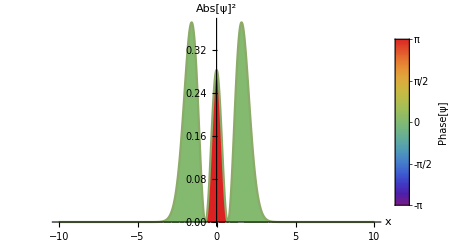

```mathematica
PlotWavefunction[ϕ[[3]], {-10, 10}, PlotRange -> All]
```

```mathematica
(grid[[2]] - grid[[1]]) Total[ Abs[ϕ[[2]]]^2]
```

1.

```mathematica
ClearAll[grid, λ, ϕ]
```

Can pass a low NumberOfPoints to make a terrible approximation

```mathematica
GetEigenmodes[1/2 x^2, {x, -10, 10}, NumberOfModes -> 1, NumberOfPoints -> 10, AutoNormalize -> False]
```

{{-10.,-7.77778,-5.55556,-3.33333,-1.11111,1.11111,3.33333,5.55556,7.77778,10.},{0.732252},{{-2.40593×10^-11,6.08138×10^-6,0.000239875,-0.0176173,-0.706887,-0.706887,-0.0176173,0.000239875,6.08138×10^-6,-2.40594×10^-11}}}

Return InterpolatingFunctions (supported by all other EigenFunctions.m methods) by passing OutputAsFunctions

```mathematica
GetEigenmodes[1/2 x^2, {x, -10, 10}, OutputAsFunctions -> True][[2;;]]
```

{{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### functions

```mathematica
GetEigenmodes[
	1/2#^2&, { -10, 10}, 
	OutputAsFunctions -> True, 
	NumberOfModes -> 4
][[2;;]]
```

{{0.5,1.5,2.5,3.5},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### vectors

```mathematica
GetEigenmodes[
	Function[x, 1/2 x^2] /@ Range[-10, 10, .1], { -10, 10}, 
	OutputAsFunctions -> True, 
	NumberOfModes -> 4
][[2;;]]
```

{{0.499999,1.49999,2.49997,3.49993},{InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>],InterpolatingFunction[{{-10., 10.}}, <>]}}

### constants

Note potentials are superposed with an infinite potential well with barriers at the edges of the given domain. Constant passed Potentials are thus really box potentials

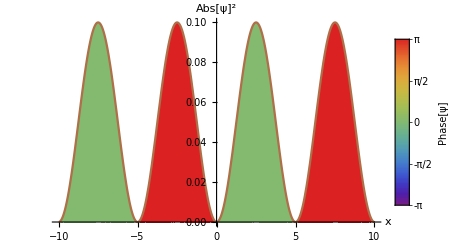

```mathematica
GetEigenmodes[
	4, 
	{-10, 10}
];
PlotWavefunction[%[[3,4]], {-10, 10}]
```

Non-box potentials are effectively approximated by potentials with grow large before the boundaries, on a sufficiently large domain

## Plotting eigenmodes (given)

### vectors

```mathematica
PlotSpectrum[
	{ -5, 5},     (* domain *)
	{1, 1/3, "ⅈ"},  (* eigvals *)
	{{1,1,1,1,1}, {2, 2, 2, 2, 2}, {1.5, 1.5, 1.5, 1.5, 1.5}},  (* eig funcs *)
	PlotRange -> {0,5}
]
```

### functions

```mathematica
PlotSpectrum[
	{x, -5, 5},
	 {1, 2}, 
	{(1&), (2&)},
	 PlotRange -> {0,5},  (* Plot option *)
	Paneled -> True,            (* Manipulate option *)
	LegendLayout -> "Row"  (* BarLegend option *)
	
]
```

### symbolic expressions

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {"π", "2π"}, 
	{Exp[-x^2]Exp[x ⅈ],Exp[-x^4]x + .3 ⅈ},
	PlotRange -> {{-2, 2}, {0, 1}}
]
```

### mixed

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {1, 2, 4, 5}, 
	{5, x^3, (#&), {1, 2, 3, 4, 5}},
	Paneled -> False
]
```

### wrapped (passing {domain/grid, eigvals, eigfuncs})

Eigenmodes outputs {grid, eigvals, eigfuncs}

```mathematica
PlotSpectrum[
	GetEigenmodes[x^2/2, {x, -10, 10}]
]
```

```mathematica
PlotSpectrum[
	GetEigenmodes[x^2/2, {x, -10, 10}, OutputAsFunctions -> True]
]
```

## Plotting eigenmodes (to be computed)

### functions

```mathematica
PlotSpectrum[
	(#&), {0, 10}, NumberOfPoints -> 100
]
```

### symbolic

```mathematica
PlotSpectrum[
	1/2 x^2, {x, -10, 10},
	PlotRange -> {{-5, 5}, {0, 1}},   (* Plot option *)
	NumberOfModes -> 3,                                 (* GetEigenmodes option *)
	ColorScheme -> "BrightBands",          (* PlotWavefunction option *)
	Paneled -> True,                                       (* Manipulate option *)
	PotentialTransform -> (#/12&),  (* PlotWavefunction options... *)
	PotentialPlotOptions -> {PlotStyle -> Blue}
]
```

### vectors

```mathematica
PlotSpectrum[
	Range[1, 10, .01],
	{0, 10},
	PotentialTransform -> (#/10&)
]
```

### constants

```mathematica
PlotSpectrum[
	0.5,
	{x, 0, 1}
]
```

### other stuff

potential plot can be overridden, separating numerics and aesthetics

```mathematica
PlotSpectrum[
	0.5,
	{x,-3, 3},
	Potential -> x^2,
	PotentialTransform -> (#/20&),
	PotentialPlotOptions -> {PlotStyle -> Blue}
]
```

## Doesn’t match

The same rules of the Potential specification in PlotFunctions.m apply here

```mathematica
PlotSpectrum[x^2, { -10, 10}]
PlotSpectrum[#2&, { -10, 10}]
```

PlotSpectrum[x^2,{-10,10}]

PlotSpectrum[#2&,{-10,10}]

Unequal number of eigenvalues and eigenfunctions

```mathematica
PlotSpectrum[
	{x,  -5, 5},
	 {1, 2, 4, 5, 6}, 
	{x^2, x^3, (#&), {1, 2, 3, 4, 5}},
	Paneled -> False
]
```

PlotSpectrum[{x,-5,5},{1,2,4,5,6},{x^2,x^3,#1&,{1,2,3,4,5}},Paneled→False]

One of the eigenfunctions is symbolic, but a symbol isn’t specified in the domain

```mathematica
PlotSpectrum[
	{-5, 5},
	 {1, 2, 3}, 
	{(#&), x y z, {1, 2, 3, 4, 5}}
]
```

PlotSpectrum[{-5,5},{1,2,3},{#1&,x y z,{1,2,3,4,5}}]

## Throws error

```mathematica
GetEigenmodes[x^2, {x, -5, 5}, poop -> 9];
```

OptionValue::nodef: Unknown option poop for GetEigenmodes.

PlotSpectrum, if passed a potential, accepts options for GetEigenmodes, Manipulate, and all the plotting functions associated with PlotWavefunction

```mathematica
PlotSpectrum[
	1/2 x^2, {x, -10, 10},
	NumberOfModes -> 3, 
	Paneled -> True,
	 poop -> 9
]
```

OptionValue::nodef: Unknown option poop for {PlotWavefunction,BarLegend,Plot,GetEigenmodes,Manipulate}.

However, if passing the eigenfunctions directly, PlotSpectrum will not accept GetEigenmodes options

```mathematica
PlotSpectrum[
	{x, -10, 10},
	{1, 2, 3},
	{x Exp[-x], Exp[-x^2], x Exp[-x^2]},
	NumberOfModes -> 2,
	poop -> 9
]
```

OptionValue::nodef: Unknown option NumberOfModes for {PlotWavefunction,BarLegend,Plot,Manipulate}.

OptionValue::nodef: Unknown option poop for {PlotWavefunction,BarLegend,Plot,Manipulate}.

```mathematica
GetEigenmodes[x^2/2, {x, -10, 10}, NumberOfPoints ->1];
```

GetEigenmodes::numPointsLessThanTwoError: NumberOfPoints given to GetEigenmodes (1) too small; must be at least 2. Using NumberOfPoints -> 10001 instead.

```mathematica
GetEigenmodes[x^2/2, {x, -10, 10}, NumberOfPoints ->3, NumberOfModes -> 20];
```

GetEigenmodes::numPointsLessThanNumModesError: NumberOfPoints given to GetEigenmodes (3) is less than NumberOfModes (20). Using NumberOfPoints -> 10001 instead.

## Two Dimensions

## Normalizing wavefunctions

### constants

Passing a domain means the wavefunction is assumed to drop to 0 from the constant value outside the domain

```mathematica
NormalizeWavefunction[10 ⅈ + 14, {x, 0, 10}, {y, 0, 10}]
Integrate[Abs[%]^2, {x, 0, 10}, {y, 0, 10}]
```

(7/10+ⅈ/2)/(√74)

1

Constants normalise to 0 on infinite domains

```mathematica
NormalizeWavefunction[2, {-∞,1}, {0, 1}]
```

0

### matrices

Passing a (not necessarily square) matrix of wavefunction values and the grid-spacing in the x and y directions (positive real numbers) assumes the wavefunction is zero outside the length x-grid-spacing * (Dimensions[matrix, 2] - 1) and  y-grid-spacing * (Dimensions[matrix, 1] - 1) domains

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),   (* wavefunction values *)
	1 , 2                                 (* grid spacings *)
] // MatrixForm

1*2 Total[Abs[%]^2, 2] // N
```

(1/(√2282) | √(2/1141) | 3/(√2282) | 2 √(2/1141) | 5/(√2282)
3 √(2/1141) | √(7/326) | 4 √(2/1141) | 9/(√2282) | 0
11/(√2282) | 0 | -13/(√2282) | ⅈ/(√2282) | 0
4 √(2/1141) | ⅈ √(2/1141) | 4 √(2/1141) | √(7/326) | 4 √(2/1141)
4 √(2/1141) | 4 √(2/1141) | 4 √(2/1141) | 4 √(2/1141) | 4 √(2/1141))

1.

Passing a single grid-spacing will assume the same spacing in the x and y directions

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),   (* wavefunction values *)
	3                                 (* grid spacing *)
] // MatrixForm

3 * 3Total[Abs[%]^2, 2] // N
```

(1/(3 √1141) | 2/(3 √1141) | 1/(√1141) | 4/(3 √1141) | 5/(3 √1141)
2/(√1141) | (√(7/163))/3 | 8/(3 √1141) | 3/(√1141) | 0
11/(3 √1141) | 0 | -13/(3 √1141) | ⅈ/(3 √1141) | 0
8/(3 √1141) | (2 ⅈ)/(3 √1141) | 8/(3 √1141) | (√(7/163))/3 | 8/(3 √1141)
8/(3 √1141) | 8/(3 √1141) | 8/(3 √1141) | 8/(3 √1141) | 8/(3 √1141))

1.

Passing a matrix of wavefunction values and uniform lists of x and y values (with lengths which match the number of columns and rows in the matrix) will assume the wavefunction is 0 outside the list extrema.

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5, 1, 2}, {6, 7, 8, 9, 0, 1, 2}, {11, 0, -13, ⅈ, 0, 1, 1}, {8, 2ⅈ, 8, 7, 8, 1, 2}, {8, 8, 8, 8, 8, 2, 3}}),   (* wavefunction values *)
	{0, 1, 2, 3, 4, 5, 6},       (* x values *)
	{0, 1, 2, 3, 4}                          (* y values *)
] // MatrixForm

1 * 1 * Total[Abs[%]^2, 2] // N
```

(1/(√1171) | 2/(√1171) | 3/(√1171) | 4/(√1171) | 5/(√1171) | 1/(√1171) | 2/(√1171)
6/(√1171) | 7/(√1171) | 8/(√1171) | 9/(√1171) | 0 | 1/(√1171) | 2/(√1171)
11/(√1171) | 0 | -13/(√1171) | ⅈ/(√1171) | 0 | 1/(√1171) | 1/(√1171)
8/(√1171) | (2 ⅈ)/(√1171) | 8/(√1171) | 7/(√1171) | 8/(√1171) | 1/(√1171) | 2/(√1171)
8/(√1171) | 8/(√1171) | 8/(√1171) | 8/(√1171) | 8/(√1171) | 2/(√1171) | 3/(√1171))

1.

Passing a single grid will assume the grid applies to both the x and y directions

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),   (* wavefunction values *)
	{0, 1, 2, 3, 4}       (* x and y values *)                       
] // MatrixForm

1 * 1 * Total[Abs[%]^2, 2] // N
```

(1/(√1141) | 2/(√1141) | 3/(√1141) | 4/(√1141) | 5/(√1141)
6/(√1141) | √(7/163) | 8/(√1141) | 9/(√1141) | 0
11/(√1141) | 0 | -13/(√1141) | ⅈ/(√1141) | 0
8/(√1141) | (2 ⅈ)/(√1141) | 8/(√1141) | √(7/163) | 8/(√1141)
8/(√1141) | 8/(√1141) | 8/(√1141) | 8/(√1141) | 8/(√1141))

1.

Passing a matrix of wavefunction values and x and y domains (endpoints) assumes the wavefunction is zero beyond the endpoints

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),
	{ 0, 2},
	{0, 7}
] // MatrixForm

(2/4) (7/4)* Total[Abs[%]^2, 2] // N
```

((2 √(2/163))/7 | (4 √(2/163))/7 | (6 √(2/163))/7 | (8 √(2/163))/7 | (10 √(2/163))/7
(12 √(2/163))/7 | 2 √(2/163) | (16 √(2/163))/7 | (18 √(2/163))/7 | 0
(22 √(2/163))/7 | 0 | -(26 √(2/163))/7 | 2/7 ⅈ √(2/163) | 0
(16 √(2/163))/7 | 4/7 ⅈ √(2/163) | (16 √(2/163))/7 | 2 √(2/163) | (16 √(2/163))/7
(16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7)

1.

(redundant Symbols can be passed, to clarify the dimensions)

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),
	{ x, 0, 2},
	{y, 0, 7}
] // MatrixForm

(2/4) (7/4)* Total[Abs[%]^2, 2] // N
```

((2 √(2/163))/7 | (4 √(2/163))/7 | (6 √(2/163))/7 | (8 √(2/163))/7 | (10 √(2/163))/7
(12 √(2/163))/7 | 2 √(2/163) | (16 √(2/163))/7 | (18 √(2/163))/7 | 0
(22 √(2/163))/7 | 0 | -(26 √(2/163))/7 | 2/7 ⅈ √(2/163) | 0
(16 √(2/163))/7 | 4/7 ⅈ √(2/163) | (16 √(2/163))/7 | 2 √(2/163) | (16 √(2/163))/7
(16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7 | (16 √(2/163))/7)

1.

Passing a single domain means the domain is assumed to apply in both the x and y directions

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),
	{ 0, 2}
] // MatrixForm

(2/4) (2/4)* Total[Abs[%]^2, 2] // N
```

(2/(√1141) | 4/(√1141) | 6/(√1141) | 8/(√1141) | 10/(√1141)
12/(√1141) | 2 √(7/163) | 16/(√1141) | 18/(√1141) | 0
22/(√1141) | 0 | -26/(√1141) | (2 ⅈ)/(√1141) | 0
16/(√1141) | (4 ⅈ)/(√1141) | 16/(√1141) | 2 √(7/163) | 16/(√1141)
16/(√1141) | 16/(√1141) | 16/(√1141) | 16/(√1141) | 16/(√1141))

1.

An infinite-area domain yields a 0 finitely-specified matrix

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),
	{ 0, ∞}, {0, 3}
] // MatrixForm
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}}),
	{-∞, -1}
] // MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

Passing no domain specification assumes a grid-spacing of 1 in both the x and y directions

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {11, 0, -13, ⅈ, 0}, {8, 2ⅈ, 8, 7, 8}, {8, 8, 8, 8, 8}})
] // MatrixForm
Total[Abs[%]^2, 2] // N
```

(1/(√1141) | 2/(√1141) | 3/(√1141) | 4/(√1141) | 5/(√1141)
6/(√1141) | √(7/163) | 8/(√1141) | 9/(√1141) | 0
11/(√1141) | 0 | -13/(√1141) | ⅈ/(√1141) | 0
8/(√1141) | (2 ⅈ)/(√1141) | 8/(√1141) | √(7/163) | 8/(√1141)
8/(√1141) | 8/(√1141) | 8/(√1141) | 8/(√1141) | 8/(√1141))

1.

### functions

A passed function is assumed 0 outside the passed domains

```mathematica
NormalizeWavefunction[
	(Exp[-#1^2]+ #2 &),
	{-1, 1},
	{-2, 2}
]

NIntegrate[Abs[%[x, y]]^2, {x, -1, 1}, {y, -2, 2}]
```

((Exp[-#1^2]+#2&)[#1,#2])/3.93088&

1.

A 2D function passed with a single domain means the domain is assumed to apply to both dimensions

```mathematica
NormalizeWavefunction[
	(Exp[-#1^2]+ #2 &),
	{-1,1}
]

NIntegrate[Abs[%[x, y]]^2, {x, -1, 1}, {y, -1, 1}]
```

((Exp[-#1^2]+#2&)[#1,#2])/1.93026&

1.

Passing a function and numerical grids will normalise using (bad) Riemann Summation, sampling the function on the grids

```mathematica
Evaluate @ NormalizeWavefunction[
	(Exp[-#1^2 + #2^2]&),
	Table[i, {i, -1, 1, .01}],
	Table[i, {i, -2, 2, .005}]
]
NIntegrate[Abs[%[x, y]]^2, {x, -1, 1}, {y, -2, 2}]
```

((Exp[-#1^2+#2^2]&)[#1,#2])/31.3578&

0.980624

a single passed grid will be assumed to apply to both the x and y directions

```mathematica
Evaluate @ NormalizeWavefunction[
	(Exp[-#1^2 - #2^2]&),
	Table[i, {i, -1, 1, .01}]
]
NIntegrate[Abs[%[x, y]]^2, {x, -1, 1}, {y, -1, 1}]
```

((Exp[-#1^2-#2^2]&)[#1,#2])/1.19763&

0.997756

If no domains are passed, the domain is assumed infinite in both directions, in both dimensions

```mathematica
NormalizeWavefunction[
	Function[{x, y}, Exp[-x^2-y^2]]
]

NIntegrate[Abs[%[x, y]]^2, {x, -∞, ∞}, {y, -∞, ∞}]
```

(Function[{x,y},Exp[-x^2-y^2]][#1,#2])/1.25331&

1.

### symbolic expressions

Symbolic expressions are assumed 0 outside the passed domain

```mathematica
NormalizeWavefunction[
	x y Exp[-x^2],
	{x, -5, 5},
	{y, -5, 5}
]

Integrate[Abs[%]^2, {x, -5, 5}, {y, -5, 5}]
```

2/5 ⅇ^(25-x^2) x y √(3/(5 (-20+ⅇ^50 √(2 π) Erf[5 √2])))

1

```mathematica
NormalizeWavefunction[
	x  Exp[-x^2 - y^2],
	{x, -∞, ∞},
	{y, -∞, ∞}
]

Integrate[Abs[%]^2, {x, -∞, ∞}, {y, -∞, ∞}]
```

2 ⅇ^(-x^2-y^2) √(2/π) x

1

```mathematica
MatchQ[x Exp[-x^2 - y^2], _?WavefunctionSolver`EigenFunctions`PackagePrivate`symbolicQ]
```

True

Passing no domain (passing only the Symbol, or a list containing only a Symbol) will assume a (-∞, ∞) domain

```mathematica
NormalizeWavefunction[x Exp[-x^2 - y^2], x, y]
Integrate[Abs[%]^2, {x, -∞, ∞}, {y, -∞, ∞}]

NormalizeWavefunction[x Exp[-x^2 - y^2], {x}, {y}]
Integrate[Abs[%]^2, {x, -∞, ∞}, {y, -∞, ∞}]
```

2 ⅇ^(-x^2-y^2) √(2/π) x

1

2 ⅇ^(-x^2-y^2) √(2/π) x

1

### Won’t match

The dimensions (columns and rows) of the matrix do not match the lengths of the x and y values

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5, 1, 2}, {6, 7, 8, 9, 0, 1, 2}, {11, 0, -13, ⅈ, 0, 1, 1}, {8, 2ⅈ, 8, 7, 8, 1, 2}, {8, 8, 8, 8, 8, 2, 3}}),   (* wavefunction values *)
	{0, 1, 2, 3, 4, 5, 6},       (* x values *)
	{0, 1, 2, 3}                              (* y values *)
]
```

NormalizeWavefunction[{{1,2,3,4,5,1,2},{6,7,8,9,0,1,2},{11,0,-13,ⅈ,0,1,1},{8,2 ⅈ,8,7,8,1,2},{8,8,8,8,8,2,3}},{0,1,2,3,4,5,6},{0,1,2,3}]

The dimensions (columns and rows) of the (problematically non-square) matrix do not match the lengths of the x and y values, once the un-passed y values are assumed to be the same as the passed x values

```mathematica
NormalizeWavefunction[
	({{1, 2, 3, 4, 5, 1, 2}, {6, 7, 8, 9, 0, 1, 2}, {11, 0, -13, ⅈ, 0, 1, 1}, {8, 2ⅈ, 8, 7, 8, 1, 2}, {8, 8, 8, 8, 8, 2, 3}}),   (* wavefunction values *)
	{0, 1, 2, 3, 4, 5, 6}       (* x values *)                       
]
```

NormalizeWavefunction[{{1,2,3,4,5,1,2},{6,7,8,9,0,1,2},{11,0,-13,ⅈ,0,1,1},{8,2 ⅈ,8,7,8,1,2},{8,8,8,8,8,2,3}},{0,1,2,3,4,5,6}]

```mathematica
With[
	{x = 2 + 2},
	# + x &
]
```

#1+4&